# Fast piecewise linear approximation to exponential

## John S. McCaskill Research Fellow at ECLT, Venice

```mathematica
expln2mx1[x_]:= Module[{ix,rx},
ix = Floor[x];
rx =x-ix;
2^-(ix+1)*(2.-rx)
]
```

```mathematica
expln2mx[x_]:= 2.^(-x)
```

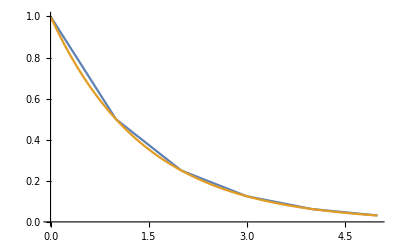

```mathematica
Plot[{expln2mx1[x],expln2mx[x]},{x,0,5}]
```

```mathematica
expln2mx2[x_]:= Module[{ix,rx},
ix = Ceiling[x];
rx =x-ix;
2^-ix*(1.-rx)
]
```

```mathematica
Plot[{expln2mx2[x],expln2mx[x]},{x,0,5}]
```

-Graphics-

```mathematica
expln2mx3[x_]:= Module[{ix,rx},
ix = Ceiling[x];
rx =x-ix;
2^-ix*Floor[65635.*(1.-rx)]
]
```

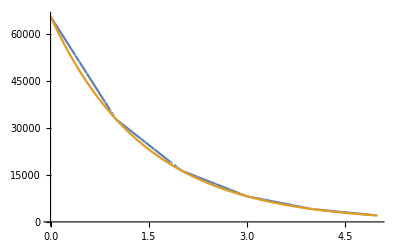

```mathematica
Plot[{expln2mx3[x],65635*expln2mx[x]},{x,0,5}]
```